```mathematica
Clear["Global`*"]
```

```mathematica
z = R Sin[θ] ⅈ + R Cos[θ]+0.5;
circularmap[] = z μ (1 - z)
circularmap[circularmap[circularmap[z]]]
```

μ (0.5-R Cos[θ]-ⅈ R Sin[θ]) (0.5+R Cos[θ]+ⅈ R Sin[θ])

μ (1-R Cos[θ]-ⅈ R Sin[θ]) (R Cos[θ]+ⅈ R Sin[θ])

```mathematica
Conver
```

```mathematica
circularmap[μ (1-R Cos[θ]-ⅈ R Sin[θ]) (R Cos[θ]+ⅈ R Sin[θ])]
```

μ (1-R Cos[θ]-ⅈ R Sin[θ]) (R Cos[θ]+ⅈ R Sin[θ])

```mathematica
Assuming[{R>0,μ>0, θ>0},ComplexExpand[μ (0.5-R Cos[θ]-ⅈ R Sin[θ]) (0.5+R Cos[θ]+ⅈ R Sin[θ]), TargetFunctions->{Abs, Arg}]]
```

0.+0.25 μ-R^2 μ Cos[θ]^2+R^2 μ Sin[θ]^2+ⅈ (0.-2 R^2 μ Cos[θ] Sin[θ])

```mathematica
FullSimplify[ArcTan[(R μ Sin[θ]-2 R^2 μ Cos[θ] Sin[θ])/(R μ Cos[θ]-R^2 μ Cos[θ]^2+R^2 μ Sin[θ]^2)]/.R-> 1/2]
```

-ArcTan[(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])]

```mathematica
FullSimplify[(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])]
```

(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])

```mathematica
TeXForm[(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])]
```

\frac{2 \sin (\theta ) (\cos (\theta )-1)}{2 \cos (\theta )-\cos (2 \theta )}

```mathematica
FullSimplify[√((R μ Sin[θ]-2 R^2 μ Cos[θ] Sin[θ])^2+(R μ Cos[θ]-R^2 μ Cos[θ]^2+R^2 μ Sin[θ]^2)^2)]
```

√(R^2 μ^2 (1+R^2-2 R Cos[θ]))

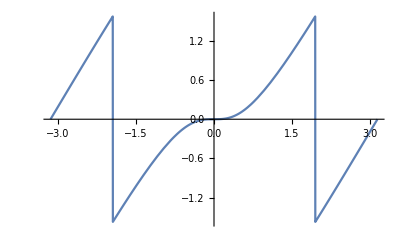

```mathematica
Plot[ArcTan[((-1+2 R Cos[θ]) Sin[θ])/(-Cos[θ]+R Cos[2 θ])]/.R-> 0.5, {θ,-π, π}]
```

```mathematica
Abs[ⅇ^(ⅈ θ)/. θ-> π/2]
```

1

```mathematica
xn[x_,y_,μ_] = x μ - x^2 μ + y^2 μ;
yn[x_,y_,μ_] = y μ -2 x y μ;
```

```mathematica
μ = 3.8284;
rn1[r_,θ_] =√(xn[r Cos[θ], r Sin[θ],μ]^2 + yn[r Cos[θ], r Sin[θ],μ]^2);
θn1[r_,θ_]= ArcTan[yn[r Cos[θ], r Sin[θ],μ]/xn[r Cos[θ], r Sin[θ],μ]];
```

```mathematica
colourplotcircle={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ-x^2 μ+y^2 μ;
yn[x_,y_] = y μ-2 x y μ;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,y1}]];
AppendTo[colourplotcircle,locallistcircle]]
```

```mathematica
μ = 3.8284;
listcircle = {};
For[R = 0, R<0.5,R+=0.02;
localcircle={};
For[θ=0, θ<2 Pi, θ+=0.1/(R+1);
x = R Cos[θ]+ 0.9578797642117602;
y = R Sin[θ];
AppendTo[localcircle,{x,y}]];
AppendTo[listcircle, localcircle]]
```

```mathematica
μ = 3.8284;
listcircle = {};
For[R = 0, R<0.5,R+=0.02;
localcircle={};
For[θ=0, θ<2 Pi, θ+=0.1/(R+1);
x = R Cos[θ]+0.5;
y = R Sin[θ];
AppendTo[localcircle,{x,y}]];
AppendTo[listcircle, localcircle]]
```

```mathematica
Length[listcircle]
```

500

```mathematica
Timing[circlemap0={};
For[i=0,i<Length[listcircle],i++;
localcircle=ListPlot[listcircle⟦i⟧,PlotStyle->Hue[i/(1.15Length[listcircle])]];
AppendTo[circlemap0,localcircle]];]
```

{0.360159,Null}

```mathematica
Timing[circlemap2 = Table[ListPlot[listcircle⟦i⟧,PlotStyle->Hue[i/(1.15Length[listcircle])]],{i,1,Length[listcircle]}];]
```

{12.3554,Null}

```mathematica
Show[circlemap2, PlotRange-> All]
```

-Graphics-

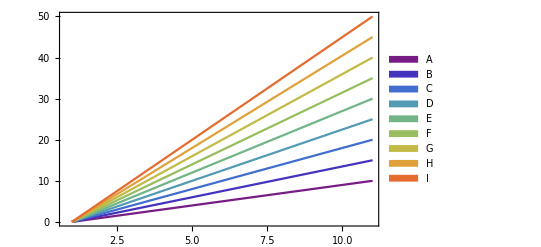

```mathematica
d=Table[i Range[0,10],{i,1,5,0.5}];
ListPlot[d,Frame->True,Joined->True,PlotRange->All,PlotLegends->SwatchLegend[Characters["ABCDEFGHIGKLMNOP"]],PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@d]/Length@d)]
```

```mathematica
d
```

{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{0.,1.5,3.,4.5,6.,7.5,9.,10.5,12.,13.5,15.},{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.,20.},{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.},{0.,3.,6.,9.,12.,15.,18.,21.,24.,27.,30.},{0.,3.5,7.,10.5,14.,17.5,21.,24.5,28.,31.5,35.},{0.,4.,8.,12.,16.,20.,24.,28.,32.,36.,40.},{0.,4.5,9.,13.5,18.,22.5,27.,31.5,36.,40.5,45.},{0.,5.,10.,15.,20.,25.,30.,35.,40.,45.,50.}}

```mathematica
Timing[ d=Table[i*Range[0,10],{i,1,30,0.5}];
ListPlot[listcircle,PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@d]/Length@d)]]
```

{17.6963,-Graphics-}

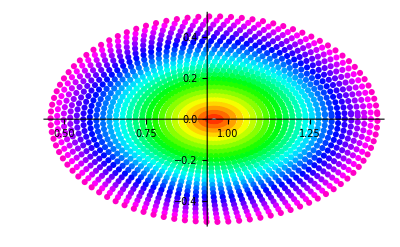
{0.000167,-Graphics-}

```mathematica
Timing[Show[circlemap0,PlotRange->All]]
```

```mathematica
colourplotcircle={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ-x^2 μ+y^2 μ;
yn[x_,y_] = y μ-2 x y μ;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{xlocal,x1}]];
AppendTo[colourplotcircle,locallistcircle]]
```

```mathematica
colourplotcircle={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ-x^2 μ+y^2 μ;
yn[x_,y_] = y μ-2 x y μ;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,xlocal,y1}]];
AppendTo[colourplotcircle,locallistcircle]]
```

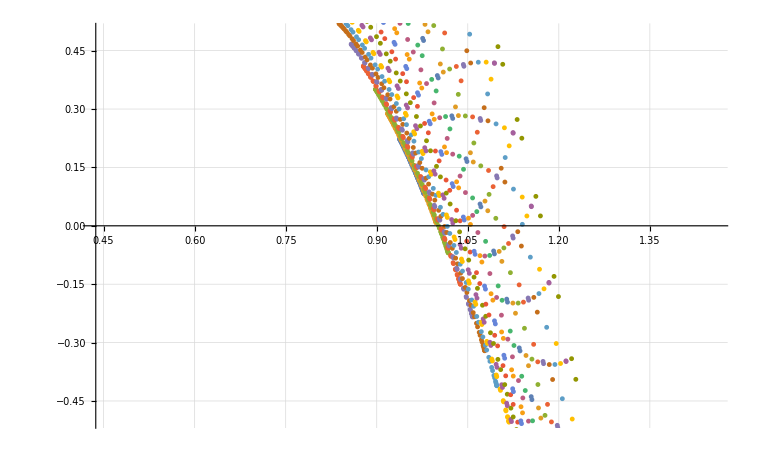

```mathematica
ListPlot[colourplotcircle, GridLines->Automatic, PlotRange->{-0.5,0.5}]
```

```mathematica
colourplotcircle
```

{{{0.519904,0.00195764,0.955598},{0.519617,0.00389649,0.955685},{0.519141,0.00579791,0.955826},{0.518482,0.00764365,0.956016},58,{0.519886,-0.00213025,0.955603},{0.519999,-0.000173508,0.955569},{0.51992,0.0017849,0.955593}},23,{1}}
 |  |  |  |

```mathematica
circlemap1={};
For[i=0,i<Length[colourplotcircle],i++;
localcircle=ListPlot[colourplotcircle⟦i⟧,PlotStyle->Hue[i/(1.15Length[colourplotcircle])]];
AppendTo[circlemap1,localcircle]];
```

```mathematica
Show[circlemap1,PlotRange->Automatic, Frame-> True]
```

-Graphics-

```mathematica
colourplotcircle2={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] =x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
yn[x_,y_] = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,y1}]];
AppendTo[colourplotcircle2,locallistcircle]]
```

```mathematica
circlemap2={};
For[i=0,i<Length[colourplotcircle2],i++;
localcircle=ListPlot[colourplotcircle2⟦i⟧,PlotStyle->Hue[i/(1.15Length[colourplotcircle2])]];
AppendTo[circlemap2,localcircle]];
```

```mathematica
colourplotcircle3={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x3 ,y3}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x3,y3}]];
AppendTo[colourplotcircle3,locallistcircle]]
```

```mathematica
circlemap3={};
For[i=0,i<Length[colourplotcircle3],i++;
localcircle=ListPlot[colourplotcircle3⟦i⟧,PlotStyle->Hue[i/(1.15Length[colourplotcircle3])]];
AppendTo[circlemap3,localcircle]];
```

```mathematica
Show[circlemap0,PlotRange-> {{0,1},{-0.1,0.1}}, Frame-> True, GridLines-> Automatic]
```

```mathematica
Show[circlemap3,PlotRange-> {{0,1},{-0.1,0.1}}, Frame-> True,GridLines-> Automatic]
```

-Graphics-

```mathematica
circlemap0={};
For[i=0,i<Length[listcircle],i++;
localcircle={};
For[j=0,j<Length[listcircle⟦i⟧], j++;
pointcircle=ListPointPlot3D[{listcircle⟦i,j⟧},PlotStyle->{Hue[i/(1.15Length[listcircle])],Opacity[0.05+j/(2.25Length[listcircle⟦i⟧])]}];
AppendTo[localcircle,pointcircle]];
AppendTo[circlemap0,localcircle]];
```

```mathematica
circlemap1={};
For[i=0,i<Length[colourplotcircle],i++;
localcircle={};
For[j=0,j<Length[colourplotcircle⟦i⟧], j++;
pointcircle=ListPointPlot3D[{colourplotcircle⟦i,j⟧},PlotStyle->{Hue[i/(1.15Length[colourplotcircle])],Opacity[0.05+j/(2.25Length[colourplotcircle⟦i⟧])]}];
AppendTo[localcircle,pointcircle]];
AppendTo[circlemap1,localcircle]];
```

```mathematica
circlemap1={};
For[i=0,i<Length[colourplotcircle],i++;
localcircle={};
For[j=0,j<Length[colourplotcircle⟦i⟧], j++;
pointcircle=ListSurfacePlot3D[{colourplotcircle⟦i,j⟧},PlotStyle->{Hue[i/(1.15Length[colourplotcircle])],Opacity[0.05+j/(2.25Length[colourplotcircle⟦i⟧])]}];
AppendTo[localcircle,pointcircle]];
AppendTo[circlemap1,localcircle]];
```

```mathematica
Show[circlemap1]
```

Show[{{ListSurfacePlot3D[{{0.956725,0.50995,-0.0000760586}},PlotStyle→{Hue[0.01739130434782609],Opacity[0.0570547]}],ListSurfacePlot3D[{{0.956747,0.509801,-0.000149085}},PlotStyle→{Hue[0.01739130434782609],Opacity[0.0641093]}],60,ListSurfacePlot3D[{{0.956717,0.509999,-0.0000128722}},PlotStyle→{Hue[0.01739130434782609],Opacity[0.494444]}]},48,{ListSurfacePlot3D[{{1}},1],61,1}}]
 |  |  |  |

```mathematica
Show[circlemap0,PlotRange-> All]
```

-Graphics3D-

```mathematica
Show[circlemap1,PlotRange-> {Automatic,Automatic,Automatic},AxesLabel-> {"x0", "y0", "x1"},BoxRatios-> {1, 1, 1}, ViewPoint-> {0,Infinity,0}]
```

-Graphics3D-

```mathematica
Show[circlemap1,PlotRange-> All,AxesLabel-> {"x1", "x0", "y1"},BoxRatios-> {1, 1, 1}]
```

-Graphics3D-

```mathematica
xn[0.5,0]
```

0.9571

```mathematica
colourplotcircle2={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] =x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
yn[x_,y_] = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,y1}]];
AppendTo[colourplotcircle2,locallistcircle]]
```

```mathematica
Clear["Global`*"]
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))];
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
ComplexExpand[Normal[Series[map3[1/2+ ϵ,y,μ],{ϵ,0, 1}]]]
```

μ^3/4+y^2 μ^3-μ^4/16-(y^2 μ^4)/2-y^4 μ^4-μ^5/16-(y^2 μ^5)/2-y^4 μ^5+μ^6/32+(3 y^2 μ^6)/8+(3 y^4 μ^6)/2+2 y^6 μ^6-μ^7/256-(y^2 μ^7)/16-(3 y^4 μ^7)/8-y^6 μ^7-y^8 μ^7+ⅈ (-2 y ϵ μ^3+y ϵ μ^4+4 y^3 ϵ μ^4+y ϵ μ^5+4 y^3 ϵ μ^5-3/4 y ϵ μ^6-6 y^3 ϵ μ^6-12 y^5 ϵ μ^6+1/8 y ϵ μ^7+3/2 y^3 ϵ μ^7+6 y^5 ϵ μ^7+8 y^7 ϵ μ^7)

```mathematica
FullSimplify[(-2 y ϵ μ^3+y ϵ μ^4+4 y^3 ϵ μ^4+y ϵ μ^5+4 y^3 ϵ μ^5-3/4 y ϵ μ^6-6 y^3 ϵ μ^6-12 y^5 ϵ μ^6+1/8 y ϵ μ^7+3/2 y^3 ϵ μ^7+6 y^5 ϵ μ^7+8 y^7 ϵ μ^7)]
```

1/8 y ϵ μ^3 (-2+μ+4 y^2 μ) (8+(1+4 y^2) μ^2 (-4+μ+4 y^2 μ))

```mathematica
Normal[Series[map[1/2+ ϵ,y,μ],{ϵ,0, 1}]]
```

μ/4+y^2 μ-2 ⅈ y ϵ μ

```mathematica
ComplexExpand[Normal[Series[Series[map3[1/2+ ϵ,y,μ],{ϵ,0, 3}],{y,0,2}]]]
```

μ^3/4+y^2 μ^3-ϵ^2 μ^3-μ^4/16-(y^2 μ^4)/2+(ϵ^2 μ^4)/2+6 y^2 ϵ^2 μ^4-μ^5/16-(y^2 μ^5)/2+(ϵ^2 μ^5)/2+6 y^2 ϵ^2 μ^5+μ^6/32+(3 y^2 μ^6)/8-(3 ϵ^2 μ^6)/8-9 y^2 ϵ^2 μ^6-μ^7/256-(y^2 μ^7)/16+(ϵ^2 μ^7)/16+9/4 y^2 ϵ^2 μ^7+ⅈ (-2 y ϵ μ^3+y ϵ μ^4-4 y ϵ^3 μ^4+y ϵ μ^5-4 y ϵ^3 μ^5-3/4 y ϵ μ^6+6 y ϵ^3 μ^6+1/8 y ϵ μ^7-3/2 y ϵ^3 μ^7)

```mathematica
FullSimplify[ (-2 y ϵ μ^3+y ϵ μ^4-4 y ϵ^3 μ^4+y ϵ μ^5-4 y ϵ^3 μ^5-3/4 y ϵ μ^6+6 y ϵ^3 μ^6+1/8 y ϵ μ^7-3/2 y ϵ^3 μ^7)]
```

-1/8 y ϵ (-2+μ) μ^3 (-8-(-4+μ) μ^2+4 ϵ^2 μ (-4+3 (-2+μ) μ))

```mathematica
FullSimplify[Normal[Series[Solve[(-2+μ) μ^3 (-8-(-4+μ) μ^2+4 ϵ^2 μ (-4+3 (-2+μ) μ))== 0,μ]⟦All,1,2⟧,{ϵ,0,2}]],Assumptions->ϵ>0]
```

{0,0,0,2,-(4 √2 (5 (-533857665 ⅈ √(15 (161-72 √5))-580194727 (-9+4 √5))^(1/6)+8 √5 (-580194727 (-161+72 √5)-533857665 ⅈ √3 (-360+161 √5))^(1/6) ϵ^2))/(5 (11+3 ⅈ √15)^(2/3) (-11 ⅈ+3 √15)),1+√5+(8+24/(√5)) ϵ^2,2+8 ϵ^2}

```mathematica
1.+√5
```

3.23607

```mathematica
μ^3/4+y^2 μ^3-μ^4/16-(y^2 μ^4)/2-μ^5/16-(y^2 μ^5)/2+μ^6/32+(3 y^2 μ^6)/8-μ^7/256-(y^2 μ^7)/16/.μ-> 1.+√5
```

0.809017

```mathematica
72. √5
```

160.997

```mathematica
161. √5
```

360.007

```mathematica
Solve[(y μ-2 x y μ)== 0,x]
```

{{x→1/2}}

```mathematica
yband = {y-> 0, y-> (√(-2μ x^2+ 2μ x-1))/(√(2 μ)),  y-> -(√(-2μ x^2+ 2μ x-1))/(√(2 μ)), y-> (√(1/μ+ 6 x^2-(√(μ^3(μ^3+ 2 μ^2+μ + 32 μ^3 x^4 -64 μ^3 x^3+44 μ^3  x^2 + 8 μ^2 x^2-12 μ^3 x-8 μ^2 x-2))-6x+1)/μ^3))/(√2), y->-(√(1/μ+ 6 x^2-(√(μ^3(μ^3+ 2 μ^2+μ + 32 μ^3 x^4 -64 μ^3 x^3+44 μ^3  x^2 + 8 μ^2 x^2-12 μ^3 x-8 μ^2 x-2))-6x+1)/μ^3))/(√2)}/.{x-> 1.0, μ-> 3.8}
```

{y→0,y→0.+0.362738 ⅈ,y→0.-0.362738 ⅈ,y→1.59775,y→-1.59775}

```mathematica
Plot3D[yband⟦3,2⟧,{x,0,1},{μ,3.5,3.85}]
```

-Graphics3D-

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]]
```

{{y→0},{y→-(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→-(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)}}

```mathematica
xs = Solve[im==0,x]
```

{{x→1/2},{x→(μ-√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→(μ+√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→1/2 (1-√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1-√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))}}

```mathematica
(μs = Solve[im==0,μ]);
```

```mathematica
ContourPlot[im== 0,{x,0,1},{y,-1,1}]
```

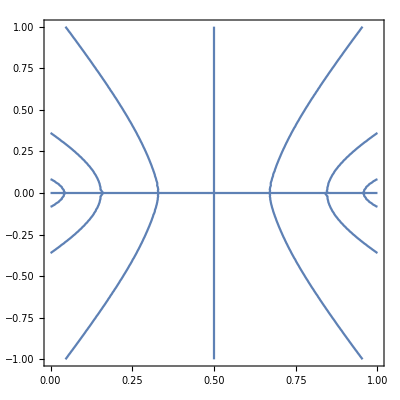

```mathematica
ContourPlot[im== 0,{x,0,1},{y,-1,1}]
```

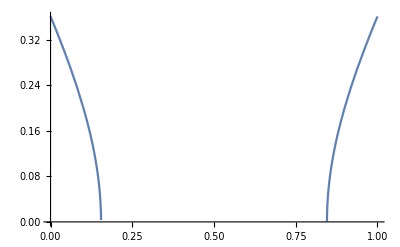

```mathematica
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1}]
```

```mathematica
g
```

```mathematica
ComplexExpand[Normal[Series[Series[ys⟦4,1,2⟧/. x->(x+1/2),{ϵ,0, 1}],{x,0,1}]]]
```

-1/2 Cos[1/2 Arg[(2 μ^2-μ^3-2 √((-2+μ) μ^3))/μ^3]] ((-1+2/μ-(2 ((-2+μ)^2 μ^6)^(1/4) Cos[1/2 Arg[(-2+μ) μ^3]])/μ^3)^2+(4 √((-2+μ)^2 μ^6) Sin[1/2 Arg[(-2+μ) μ^3]]^2)/μ^6)^(1/4)-1/2 ⅈ ((-1+2/μ-(2 ((-2+μ)^2 μ^6)^(1/4) Cos[1/2 Arg[(-2+μ) μ^3]])/μ^3)^2+(4 √((-2+μ)^2 μ^6) Sin[1/2 Arg[(-2+μ) μ^3]]^2)/μ^6)^(1/4) Sin[1/2 Arg[(2 μ^2-μ^3-2 √((-2+μ) μ^3))/μ^3]]

```mathematica
ys
```

{{y→0},{y→-(ⅈ √(-1+2 x μ-2 x^2 μ))/(√2 √μ)},{y→(ⅈ √(-1+2 x μ-2 x^2 μ))/(√2 √μ)},{y→-(√(1-6 x+6 x^2+1/μ-(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)},{y→(√(1-6 x+6 x^2+1/μ-(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)},{y→-(√(1-6 x+6 x^2+1/μ+(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)},{y→(√(1-6 x+6 x^2+1/μ+(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)}}

```mathematica
ys⟦3,1,2⟧/. x->(x0+ϵ)
```

(0.+0.36139 ⅈ) √(-1+7.6568 (x0+ϵ)-7.6568 (x0+ϵ)^2)

```mathematica
slist = Table[ComplexExpand[Normal[Series[ys⟦i,1,2⟧/. x->(x+ϵ),{ϵ,0,1}]]],{i,1,Length[ys]}]
```

$Aborted

```mathematica
3
```

```mathematica
banda1 = FullSimplify[Normal[Series[im/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0,{ϵ,0,3}]]/ ys⟦3,1,2⟧/.x-> x0]/.μ-> 3.8284
```

214.817 ϵ (1.8284 (-1+2 x0+ϵ) (-1+2 x0+2 ϵ)+2 (3.8284-7.6568 x0)^2 ((1-2 x0)^2+7 (-1+2 x0) ϵ+18 ϵ^2)+224.446 (1-2 x0)^2 ((1-2 x0)^2 (-1+x0) x0+7 (-1+x0) x0 (-1+2 x0) ϵ+(-1+14 (-1+x0) x0) ϵ^2))

```mathematica
banda05= FullSimplify[Normal[Series[im/y,{x,1/2,1}]/.μ-> 3.8284]/.x-> 1/2+ϵ]
```

(70.3402+3338.47 y^2+34540.3 y^4+96429.8 y^6) ϵ

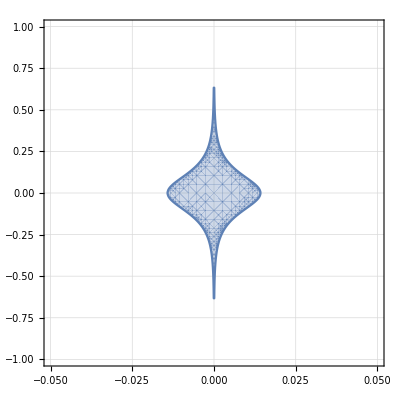

```mathematica
RegionPlot[Abs[banda05]< 1,{ϵ,-0.05,0.05},{y,-1,1},GridLines->Automatic,MaxRecursion->5]
```

```mathematica
banda312= FullSimplify[im/ys⟦3,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

Part::partd: Part specification ys⟦3,1,2⟧ is longer than depth of object.

```mathematica
banda212= FullSimplify[im/ys⟦2,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda412= FullSimplify[im/ys⟦4,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda512= FullSimplify[im/ys⟦5,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda612= FullSimplify[im/ys⟦6,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
s1 = Solve[banda1== 1,ϵ]⟦1,1,2⟧;
```

$Aborted

```mathematica
RegionPlot[Abs[banda612]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

```mathematica
RegionPlot[Abs[banda512]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

```mathematica
RegionPlot[Abs[banda412]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

```mathematica
RegionPlot[Abs[banda212]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

```mathematica
RegionPlot[Abs[banda312]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

```mathematica
Plot[s1/.μ-> 3.8284,{x0,0,1},GridLines->Automatic]
```

-Graphics-

```mathematica
Region
```